```mathematica
<< MaTeX`
```

## Dynamical evolution of PDF (Figure 2)

```mathematica
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{2,1}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

```mathematica
LTicksLog=Flatten[{Table[{Log[10^i],Superscript[10,i],{0.02,0},Thickness[0.004]},{i,-9,-1,3}],{{1,1,{0.02,0},Thickness[0.004]}},Table[{Log[10^i],,{0.01,0},Thickness[0.002]},{i,-9,-1}]},1];
STicksLog=Flatten[{Table[{Log[10^i],,{0.02,0},Thickness[0.004]},{i,-9,-1,3}],Table[{Log[10^i],,{0.01,0},Thickness[0.002]},{i,-9,-1}],{{1,,{0.01,0},Thickness[0.002]}}},1];
```

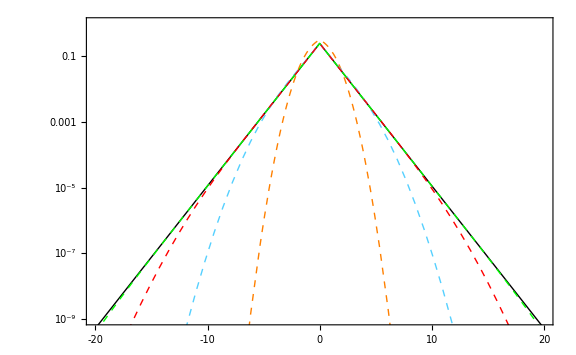

```mathematica
d=1;r1=1.0;r2=1.0;
NESS=1/2 r2/(r1+r2)Sqrt[r1/d]Exp[-Sqrt[r1/d]Abs[xvar]];
NumericIntegral[xvar_,t_]:=Exp[-r1 t] 1/Sqrt[4 Pi d t] Exp[-xvar^2/(4 d t)]+r2/(r1+r2) r1 Exp[-r1 t]NIntegrate[(Exp[r1 τ]-Exp[-r2 τ])Exp[-xvar^2/(4 d (t-τ))]/Sqrt[4 Pi d (t-τ)],{τ,0,t}]; 
NumericIntegral2[xvar_,t_]:=Exp[-r1 t] 1/Sqrt[4 Pi d t] Exp[-xvar^2/(4 d)t]+r2/(r1+r2) r1 Exp[-r1 t]NIntegrate[(Exp[r1 τ]-Exp[-r2 τ])Exp[-xvar^2/(4 d (t-τ))t^2]/Sqrt[4 Pi d (t-τ)],{τ,0,t}];
xm=-20;xM=20;Δxm=5;ΔxM=10;t1=0.5;
t2=2;t3=5;t4=10;SizeLegend=1;P1=Show[LogPlot[{NESS,NumericIntegral[xvar,t1],NumericIntegral[xvar,t2],NumericIntegral[xvar,t3],NumericIntegral[xvar,t4]},{xvar,-20,20},PlotStyle->{{Thick,Black},{Thick,Dashed,Orange},{Thick,Dashed,RGBColor[{85,208,255}/255]},{Thick,Dashed,Red},{Thick,Dashed,Green}},PlotLegends->Placed[{MaTeX["\\mbox{NESS}",Magnification->SizeLegend],MaTeX["t=0.5",Magnification->SizeLegend],MaTeX["t=2",Magnification->SizeLegend],MaTeX["t=5",Magnification->SizeLegend],MaTeX["t=10",Magnification->SizeLegend]},{0.85,0.7}],Axes->False,PlotRange->Full],PlotRange->{{-20,20},Log[{10^-9,1}]},
Frame->True,ImageSize-> Large,FrameTicks->{{LTicksLog,STicksLog} ,{LTicks[xm,xM,Δxm,ΔxM],STicks[xm,xM,Δxm,ΔxM]}},FrameLabel->{MaTeX["x",Magnification->2],MaTeX["p^{\\scriptsize\\mbox{(p)}}(x,t|x_0)",Magnification->2]} ,LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,25,FontFamily->"Times New Roman",Thickness[0.004]],Exclusions-> None]
```

## Estimation of relaxation to steady state (Figure 3, Appendix A)

```mathematica
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{2,1}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

```mathematica
LTicksLog=Flatten[{Table[{Log[10^i],Superscript[10,i],{0.02,0},Thickness[0.004]},{i,-6,-1,1}],{{1,1,{0.02,0},Thickness[0.004]}},Table[{Log[10^i],,{0.01,0},Thickness[0.002]},{i,-9,-1,1}]},1];
STicksLog=Flatten[{Table[{Log[10^i],,{0.02,0},Thickness[0.004]},{i,-6,-1,1}],Table[{Log[10^i],,{0.01,0},Thickness[0.002]},{i,-6,-1}],{{1,,{0.01,0},Thickness[0.002]}}},1];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
p0[x_,t_,d_,r1_]:=Exp[-r1 t]/Sqrt[4 Pi d t] Exp[-x^2/(4 d t)];
```

```mathematica
p1A[x_,t_,d_,r1_,r2_]:=r1 r2/(r1+r2)  * t/Sqrt[4 Pi d t]*Sqrt[Pi/(r1 t)]Exp[-Sqrt[r1/d]Abs[x]];
```

```mathematica
p1B[x_,t_,d_,r1_,r2_]:=r1 r2/(r1+r2)  * t/Sqrt[4 Pi d t]Exp[-r1 t -x^2/(4 d t)]/(x^2/(4 d t)-r1 t);
```

```mathematica
p1C[x_,t_,d_,r1_,r2_]:=r2/(r1+r2)Sqrt[r1]/(4Sqrt[d])Exp[-Sqrt[r1/d]Abs[x]]Erfc[(Sqrt[r1/d] Abs[x]/2-r1*t)/Sqrt[Sqrt[r1/d] Abs[x]/2]];
```

```mathematica
p1D2[x_,t_,d_,r1_,r2_]:=r2/(r1+r2)  * 1/(4Sqrt[d t])Sqrt[Sqrt[r1/d] Abs[x]/2]Exp[-Sqrt[r1/d]Abs[x]]Exp[(Sqrt[r1/d] Abs[x]/2-r1*t)^2/(Sqrt[r1/d] Abs[x]/2)(Sqrt[r1/d] Abs[x]/2)/(2Sqrt[r1/d]Abs[x]-3r1 t)]Erfc[Sqrt[(Sqrt[r1/d] Abs[x]/2-r1*t)^2/(Sqrt[r1/d] Abs[x]/2)(Sqrt[r1/d] Abs[x]/2)/(2Sqrt[r1/d]Abs[x]-3r1 t)]]
```

```mathematica
p1D[x_,t_,d_,r1_,r2_]:=r2/(r1+r2)  * 1/(4Sqrt[d t])Sqrt[Sqrt[r1/d] Abs[x]/2]Exp[-Sqrt[r1/d]Abs[x]]Erfc[Sqrt[(Sqrt[r1/d] Abs[x]/2-r1*t)^2/(Sqrt[r1/d] Abs[x]/2)]]
```

```mathematica
p2[x_,t_,d_,r1_,r2_]:=r1/(r1+r2)1/Sqrt[4π*d t] Exp[-r1 t]*Exp[-x^2/(4d t)]/(1+x^2/(4d*r2*t^2));
```

```mathematica
cross[t_]:=xv/.FindRoot[p1B[xv,t,dv,r1v,r2v]-p1D[xv,t,dv,r1v,r2v],{xv,1.01*Sqrt[4 dv r1v]t}];
```

### Bins = 101(on each side). r1=1 r2=2

```mathematica
runs=10000000;bins=101;a=20; dx=a/(bins-1);
```

```mathematica
pF[x_,t_,d_,r1_,r2_]:=p0[x,t,d,r1]-p2[x,t,d,r1,r2]+Limit[p1C[xLimit,t,d,r1,r2],{xLimit->x}];
```

```mathematica
pT[x_,t_,d_,r1_,r2_]:=p0[x,t,d,r1]-p2[x,t,d,r1,r2]+p1B[x,t,d,r1,r2];
```

```mathematica
pS[x_,t_,d_,r1_,r2_]:=p0[x,t,d,r1]-p2[x,t,d,r1,r2]+p1D[x,t,d,r1,r2];
```

```mathematica
pDiff2=Import["Simulations/pDiff_r1=1_0_r2=2_0_bins=101_runs=10000000.dat"];
```

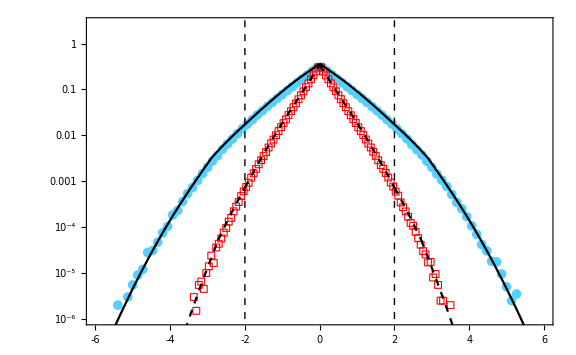

```mathematica
k1=16;k2=31;x=Range[-a-dx/2,+a+dx/2,dx]; Histx=Most[x];
Histx=x;xm=-6;xM=+6;ΔxM=2;Δxm=1;
tv1=(k1-1)*0.1;tv2=(k2-1)0.1; 
r1v=1;r2v=2;dv=1; 
cB1=Sqrt[4dv r1v];cB2=Sqrt[4dv r1v];
ColorNess=Black; 
FirstList=Most[Rest[Transpose@{Histx/tv1,pDiff2[[k1]]/runs/dx}]];SecondList=Most[Rest[Transpose@{Histx/tv2,pDiff2[[k2]]/runs/dx}]];
SimulationPlot2=Show[ListLogPlot[Select[FirstList,#[[2]]>10^-6&],PlotRange-> {{-10,10},{10^-6,1}},PlotMarkers->Style["●",RGBColor[{85,208,255}/255],Thick,10]],ListLogPlot[Select[SecondList,#[[2]]>10^-6&],PlotRange-> {{-10,10},{10^-6,1}},PlotMarkers->{Graphics[{EdgeForm[Red],FaceForm[],Rectangle[]},ImageSize-> 7]}],
LogPlot[pF[xv *tv1,tv1,dv,r1v,r2v],{xv,-cB1,cB1},PlotStyle->ColorNess,PlotRange->Full],
LogPlot[pS[xv *tv1,tv1,dv,r1v,r2v],{xv,cB1,cross[tv1]/tv1},PlotStyle->Black],
LogPlot[pS[xv *tv1,tv1,dv,r1v,r2v],{xv,-cross[tv1]/tv1,-cB1},PlotStyle->Black],
LogPlot[pT[xv *tv1,tv1,dv,r1v,r2v],{xv,cross[tv1]/tv1,xM},PlotStyle->ColorNess],
LogPlot[pT[xv *tv1,tv1,dv,r1v,r2v],{xv,xm,-cross[tv1]/tv1},PlotStyle->ColorNess], 
LogPlot[pF[xv *tv2,tv2,dv,r1v,r2v],{xv,-cB2,cB2},PlotStyle->{ColorNess,Dashed},PlotRange->Full],
LogPlot[pS[xv *tv2,tv2,dv,r1v,r2v],{xv,cB2,cross[tv2]/tv2},PlotStyle->{ColorNess,Dashed}],
LogPlot[pS[xv *tv2,tv2,dv,r1v,r2v],{xv,-cross[tv2]/tv2,-cB2},PlotStyle->{ColorNess,Dashed}],
LogPlot[pT[xv *tv2,tv2,dv,r1v,r2v],{xv,cross[tv2]/tv2,xM},PlotStyle->{ColorNess,Dashed}],
LogPlot[pT[xv *tv2,tv2,dv,r1v,r2v],{xv,xm,-cross[tv2]/tv2},PlotStyle->{ColorNess,Dashed}],
ImageSize->Large,Frame->True,Frame-> Large,FrameTicks->{{LTicksLog,STicksLog},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}} ,FrameLabel->{MaTeX["x/t",Magnification->2],MaTeX["p^{\\scriptsize\\mbox{(p)}}(x,t|x_0)",Magnification->2]} ,LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,25,FontFamily->"Times New Roman",Thickness[0.004]],Exclusions-> None,Axes-> False,
Epilog->{Directive[Black,Dashed],Line[{{-Sqrt[4 dv r1v],Log[10^-6]},{-Sqrt[4 dv r1v],Log[10]}}],Line[{{Sqrt[4 dv r1v],Log[10^-6]},{Sqrt[4 dv r1v],Log[10]}}]},PlotRange-> {{xm,xM},{Log[10^-6],1}}]
```